```mathematica
filenames={
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost0_kHerb0.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost0_kHerb5.txt",
"Table_Deterministic_control3_selfing1_sexualReproduction1_seedbank1_cost300_kCost0_kHerb10.txt"
};
```

```mathematica
data=Table[Import[NotebookDirectory[]<>"../Data/"<>filenames⟦i⟧,"CSV"],{i,Length[filenames]}];
```

```mathematica
moredata=Import[NotebookDirectory[]<>"../Data/"<>"Table_Equilibrium_tillage0.txt","CSV"]
```

{{Cost,Het,R,WW,RW,RR},{0.001,0,0.00001002,0.99999,3.99996×10^-8,0.00001},1998,{0.4,1,2.5×10^-8,1.,2.85714×10^-8,1.07143×10^-8}}
 |  |  |  |

```mathematica
pos=Position[moredata⟦All,{1,2}⟧,{0.3,0.5}]⟦1,1⟧;
```

```mathematica
onlyplants=Table[data⟦i⟧⟦2;;,{5,6,7}⟧,{i,1,Length[filenames],1}]
```

{{{3693.79,0.000147752,0.00907363},{2658.22,0.000455663,1.52734},{2530.24,0.0594804,258.791},{2432.12,8.94826,43126.9},{539.051,20.0983,1.56224×10^6},{55.8513,2.77361,1.9702×10^6},{16.514,0.830282,2.01213×10^6},{5.6587,0.286354,2.0239×10^6},{2.02259,0.102963,2.02785×10^6},{0.733506,0.0375563,2.02926×10^6},{0.267399,0.013769,2.02976×10^6},{0.0976648,0.00505726,2.02995×10^6},{0.0356957,0.00185869,2.03002×10^6},{0.0130498,0.000683264,2.03004×10^6},{0.00477124,0.000251184,2.03005×10^6},{0.00174451,0.0000923407,2.03006×10^6},{0.000637856,0.0000339455,2.03006×10^6},{0.000233224,0.0000124783,2.03006×10^6},{0.0000852756,4.58681×10^-6,2.03006×10^6},{0.00003118,1.68597×10^-6,2.03006×10^6},{0.0000114006,6.1969×10^-7,2.03006×10^6},{4.16851×10^-6,2.27762×10^-7,2.03006×10^6},{1.52417×10^-6,8.37089×10^-8,2.03006×10^6},{5.57295×10^-7,3.07643×10^-8,2.03006×10^6},{2.03769×10^-7,1.13059×10^-8,2.03006×10^6},{7.45059×10^-8,4.15478×10^-9,2.03006×10^6},{2.72423×10^-8,1.52678×10^-9,2.03006×10^6},{9.96085×10^-9,5.61032×10^-10,2.03006×10^6},{3.64208×10^-9,2.06151×10^-10,2.03006×10^6},{1.33169×10^-9,7.57472×10^-11,2.03006×10^6}},{{3693.79,0.00551805,0.00907363},{2658.22,0.471874,1.81482},{2530.13,50.2294,332.979},{2410.78,6076.,57633.7},{516.621,65920.9,1.5961×10^6},{109.337,35721.8,1.93792×10^6},{49.4145,19975.6,1.99238×10^6},{25.4251,11667.5,2.012×10^6},{13.8844,6913.17,2.02069×10^6},{7.84473,4116.64,2.02495×10^6},{4.52583,2455.77,2.02718×10^6},{2.64537,1465.93,2.0284×10^6},{1.5589,875.274,2.02909×10^6},{0.923323,522.651,2.02949×10^6},{0.548599,312.099,2.02972×10^6},{0.326588,186.371,2.02986×10^6},{0.194654,111.292,2.02994×10^6},{0.116103,66.459,2.02999×10^6},{0.0692825,39.6864,2.03001×10^6},{0.0413544,23.699,2.03003×10^6},{0.0246884,14.152,2.03004×10^6},{0.0147404,8.45098,2.03005×10^6},{0.00880145,5.04656,2.03005×10^6},{0.00525552,3.01359,2.03005×10^6},{0.00313825,1.79958,2.03006×10^6},{0.00187399,1.07463,2.03006×10^6},{0.00111905,0.641725,2.03006×10^6},{0.000668241,0.38321,2.03006×10^6},{0.000399042,0.228837,2.03006×10^6},{0.00023829,0.136651,2.03006×10^6}},{{3693.79,0.0108884,0.00907363},{2658.22,1.67022,2.10229},{2529.84,270.292,446.418},{2355.47,40976.8,85446.4},{602.332,437932.,1.37606×10^6},{355.758,375572.,1.61517×10^6},{278.346,310159.,1.70888×10^6},{225.842,257509.,1.76982×10^6},{185.982,214490.,1.81551×10^6},{154.264,179005.,1.8518×10^6},{128.451,149590.,1.88138×10^6},{107.204,125136.,1.9058×10^6},{89.606,104765.,1.92607×10^6},{74.9775,87767.8,1.94295×10^6},{62.7884,73569.2,1.95705×10^6},{52.6149,61696.1,1.96884×10^6},{44.1129,51759.2,1.9787×10^6},{37.0008,43436.8,1.98696×10^6},{31.0465,36462.5,1.99388×10^6},{26.0581,30615.,1.99968×10^6},{21.8768,25710.1,2.00455×10^6},{18.3702,21594.6,2.00863×10^6},{15.4284,18140.3,2.01206×10^6},{12.9597,15240.3,2.01494×10^6},{10.8873,12805.1,2.01735×10^6},{9.14723,10759.9,2.01938×10^6},{7.68596,9041.96,2.02109×10^6},{6.45861,7598.74,2.02252×10^6},{5.42758,6386.18,2.02372×10^6},{4.56138,5367.32,2.02473×10^6}}}

```mathematica
dominancelevels=Table[(onlyplants⟦i⟧⟦All,2⟧+2 onlyplants⟦i⟧⟦All,3⟧)/(2 (onlyplants⟦i⟧⟦All,1⟧+onlyplants⟦i⟧⟦All,2⟧+onlyplants⟦i⟧⟦All,3⟧)),{i,1,Length[filenames],1}];
```

```mathematica
prependeddominancelevels=Table[PrependTo[dominancelevels⟦i⟧ ,moredata⟦pos⟧⟦3⟧],{i,1,Length[filenames],1}];
```

```mathematica
prependeddominancelevels
```

{{4.2029×10^-8,2.47645×10^-6,0.00057433,0.0927977,0.946528,0.999649,0.999971,0.999992,0.999997,0.999999,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,3.20338×10^-6,0.000770814,0.122915,0.917593,0.979864,0.990895,0.995012,0.997105,0.998288,0.998982,0.999393,0.999638,0.999784,0.999871,0.999923,0.999954,0.999972,0.999984,0.99999,0.999994,0.999997,0.999998,0.999999,0.999999,1.,1.,1.,1.,1.,1.},{4.2029×10^-8,3.93031×10^-6,0.00110346,0.179133,0.822611,0.878999,0.905509,0.923064,0.936386,0.947083,0.955855,0.963112,0.969141,0.974163,0.978354,0.981855,0.984782,0.987233,0.989285,0.991005,0.992448,0.993658,0.994673,0.995525,0.99624,0.996841,0.997345,0.997769,0.998125,0.998424,0.998676}}

## Plot



```mathematica
ListPlot[prependeddominancelevels⟦All,1;;11⟧,Joined->True,DataRange->{0,10},PlotRange->{{-1,10.8},{-0.1,1.1}},Frame->True,PlotStyle->{Lighter[Gray],Darker[Gray],Black},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015]],PlotMarkers->{{-Graphics-,0.025},{-Graphics-,0.025},{-Graphics-,0.025}}]
```

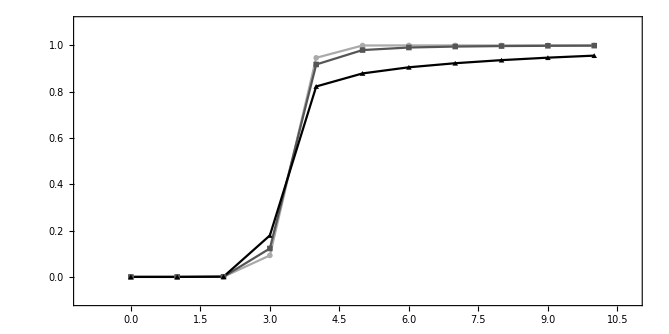

## Plot

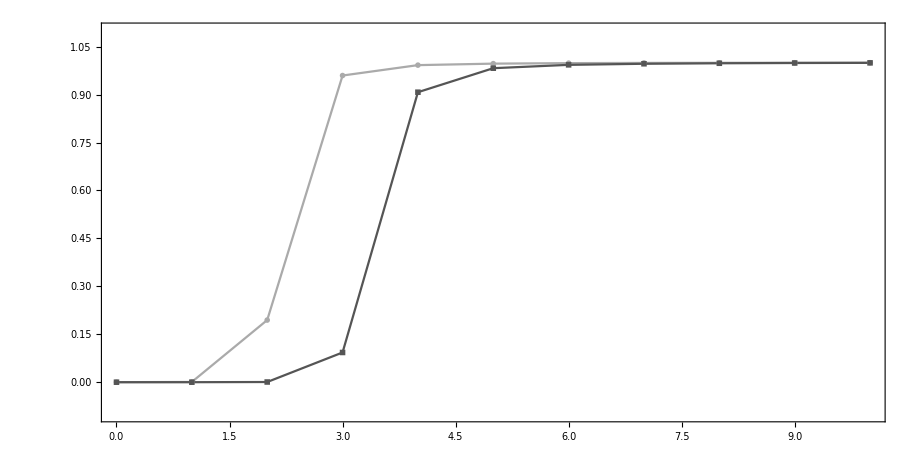

```mathematica
ListPlot[prependeddominancelevels⟦All,1;;11⟧,Joined->True,PlotRange->{All,{-0.1,1.1}},Frame->True,DataRange->{0,10},PlotMarkers->{{-Graphics-,0.025},{-Graphics-,0.025},{-Graphics-,0.025},{Graphics[{EdgeForm[{Thick,Lighter[Black]}],Lighter[Black],Rectangle[]}],0.025},{Graphics[{EdgeForm[{Thick,Lighter[Black]}],Lighter[Black],Rectangle[]}],0.025},{Graphics[{EdgeForm[Thick],Black,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}],0.025},{Graphics[{EdgeForm[Thick],Black,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}],0.025}},PlotStyle->{Lighter[Gray],Lighter[Black],Black},AspectRatio->0.5,FrameStyle->Directive[Black,Thickness[0.0015],24]]
```